Notebook author: Reed Hodges
reed.hodges@duke.edu

```mathematica
(* this file uses conventions for labeling of momenta from the PDG section on kinematics.  It is similar to a notebook by Lin Dai where he uses a different labeling convention. *)
```

```mathematica
<<MaTeX`
```

```mathematica
texStyle={FontFamily->"Times",FontSize->14};
```

# Global parameters

```mathematica
Clear[θ]
```

```mathematica
θ=-32.4Degree;
mDp=1869.66;
mD0=1864.84;
mDps=2010.26;
mD0s=2006.85;
bindingenergy=-0.273;
mT=mDps+mD0+bindingenergy;
μ0p=(1/mD0+1/mDps)^-1;
μp0=(1/mDp+1/mD0s)^-1;
γ0=√(-2μ0p(mT-mD0-mDps));
γp=√(-2μp0(mT-mDp-mD0s));
(* pion coupling diagrams *)
fπ=130.;
g=0.54;
mπ0=134.9768;
mπp=139.57039;
(* photon coupling diagrams *)
αQED=137^-1;
eQED=√(4π αQED);
β=379^-1; (* MeV^-1, look at 0511321 *)
mc=1.27*10^3;
μ1=(2eQED β)/3+(2eQED)/(3mc);
μ2=(-eQED β)/3+(2eQED)/(3mc);
μ0=√(3π mD0s/mD0 Γ/k^3)/.{Γ->19.9 10^-3,k->(mD0s^2-mD0^2)/(2mD0s)};
μp=-√(3π mDps/mDp Γ/k^3)/.{Γ->1.33 10^-3,k->(mDps^2-mDp^2)/(2mDps)};
```

# Kinematics

```mathematica
(* Follows PDG section on kinematics *)
```

```mathematica
m12[m3_,p3Sq_]:=√((mT-m3)^2-mT/m3 p3Sq);
E2[m1_,m2_,m3_,p3Sq_]:=(m12[m3,p3Sq]^2+m2^2-m1^2)/(2m12[m3,p3Sq]);
E3[m1_,m2_,m3_,p3Sq_]:=(mT^2-m3^2-m12[m3,p3Sq]^2)/(2m12[m3,p3Sq]);
p2mag[m1_,m2_,m3_,p3Sq_]:=√(E2[m1,m2,m3,p3Sq]^2-m2^2);
p3mag[m1_,m2_,m3_,p3Sq_]:=√(E3[m1,m2,m3,p3Sq]^2-m3^2);
m23SqMin[m1_,m2_,m3_,p3Sq_]:=(E2[m1,m2,m3,p3Sq]+E3[m1,m2,m3,p3Sq])^2-(p2mag[m1,m2,m3,p3Sq]+p3mag[m1,m2,m3,p3Sq])^2;
m23SqMax[m1_,m2_,m3_,p3Sq_]:=(E2[m1,m2,m3,p3Sq]+E3[m1,m2,m3,p3Sq])^2-(p2mag[m1,m2,m3,p3Sq]-p3mag[m1,m2,m3,p3Sq])^2;
p1SqMin[m1_,m2_,m3_,p3Sq_]:=m1/mT((mT-m1)^2-m23SqMax[m1,m2,m3,p3Sq]);
p1SqMax[m1_,m2_,m3_,p3Sq_]:=m1/mT((mT-m1)^2-m23SqMin[m1,m2,m3,p3Sq]);
p3SqMin[m1_,m2_,m3_]:=0;
p3SqMax[m1_,m2_,m3_]:=m3/mT((mT-m3)^2-(m1+m2)^2);
```

```mathematica
(* kinematics for dΓ/Subscript[dE, γ] which need to be modified to account for zero photon mass (since Subscript[p, 3] is assigned to photon) *)
```

```mathematica
(* Follows PDG section on kinematics *)
```

```mathematica
γm12[Eγ_]:=√(mT^2-2mT Eγ);
γE2[m1_,m2_,Eγ_]:=(γm12[Eγ]^2+m2^2-m1^2)/(2γm12[Eγ]);
γE3[m1_,m2_,Eγ_]:=(mT^2-γm12[Eγ]^2)/(2γm12[Eγ]);
γp2mag[m1_,m2_,Eγ_]:=√(γE2[m1,m2,Eγ]^2-m2^2);
γp3mag[m1_,m2_,Eγ_]:=√(γE3[m1,m2,Eγ]^2);
γm23SqMin[m1_,m2_,Eγ_]:=(γE2[m1,m2,Eγ]+γE3[m1,m2,Eγ])^2-(γp2mag[m1,m2,Eγ]+γp3mag[m1,m2,Eγ])^2;
γm23SqMax[m1_,m2_,Eγ_]:=(γE2[m1,m2,Eγ]+γE3[m1,m2,Eγ])^2-(γp2mag[m1,m2,Eγ]-γp3mag[m1,m2,Eγ])^2;
γp1SqMin[m1_,m2_,Eγ_]:=m1/mT((mT-m1)^2-γm23SqMax[m1,m2,Eγ]);
γp1SqMax[m1_,m2_,Eγ_]:=m1/mT((mT-m1)^2-γm23SqMin[m1,m2,Eγ]);
γp3SqMin[m1_,m2_,Eγ_]:=0;
γp3SqMax[m1_,m2_]:=((mT^2-(m1+m2)^2)/(2mT))^2;
```

# T_cc^+→ D^+D^0 π^0

## Γ

```mathematica
(* decay rate *)
(* assign p1=pDp and p3 = pD0 in both diagrams *)
neutralpiondecay=Module[{m1,m2,m3,pπSq,MSq,jacobian,NRnormalization},
m1=mDp;
m2=mπ0;
m3=mD0;
pπSq=(mT-m1-m3-pDpSq/(2m1)-pD0Sq/(2m3))^2-m2^2;
(*MSq=(4π g^2)/fπ^2 pπSq/3((Cos[θ] √γ0)/(pDpSq+γ0^2)-(Sin[θ] √γp)/(pD0Sq+γp^2))^2;
jacobian=mT^2/(m1 m3);
NRnormalization=(2m1)(2m3)(2mT);*)
NIntegrate[10^3(* to make result in keV *)(g^2 pπSq)/(24 fπ^2 π^2)((√γ0 Cos[θ])/(pDpSq+γ0^2)-(√γp Sin[θ])/(pD0Sq+γp^2))^2,{pD0Sq,p3SqMin[m1,m2,m3],p3SqMax[m1,m2,m3]},{pDpSq,p1SqMin[m1,m2,m3,pD0Sq],p1SqMax[m1,m2,m3,pD0Sq]},PrecisionGoal->5]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

14.5191

## dΓ/dT_(π^0)

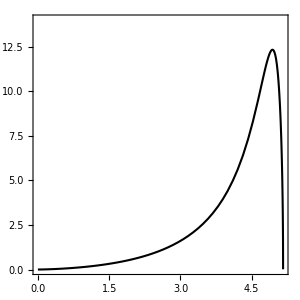

```mathematica
(* differential decay rate *)
(* assign p1=pDp and p2 = pD0 in both diagrams *)
Tπmax1=(mT^2+mπ0^2-(mDp+mD0)^2)/(2mT)-mπ0;
plotTπ1=Plot[Module[{m1,m2,m3,pD0Sq,MSq,jacobian,NRnormalization},
m1=mDp;
m2=mD0;
m3=mπ0;
pD0Sq=2m2(mT-m1-m2-pDpSq/(2m1)-√(2m3 T+m3^2));
(*MSq=(4π g^2)/fπ^2 1/3 (2m3 T)((Cos[θ] √γ0)/(pDpSq+γ0^2)-(Sin[θ] √γp)/(pD0Sq+γp^2)(*these momenta stay like they were in the full decay rate*))^2;
jacobian=(2 mT^2)/m1(* new Jacobian reflecting change from pπ^2 -> Subscript[T, π] *);
NRnormalization=(2m1)(2m2)(2mT);*)
NIntegrate[10^3(g^2 m2 m3 T)/(6 fπ^2 π^2)((√γ0 Cos[θ])/(pDpSq+γ0^2)-(√γp Sin[θ])/(pD0Sq+γp^2))^2,{pDpSq,p1SqMin[m1,m2,m3,2m3 T],p1SqMax[m1,m2,m3,2m3 T]},PrecisionGoal->5]],{T,0,Tπmax1},ImageSize->300,BaseStyle->texStyle,AspectRatio->1,FrameStyle->Black,Frame->True,PlotRange->{0,14},PlotStyle->{Black,Thickness[0.005]}]
```

```mathematica
Grid[{{Rotate[MaTeX["\\frac{d\\Gamma[T_{cc}^+ \\rightarrow D^+ D^0 \\pi^0]}{dT_{\\pi^0}}",Magnification->1.5],90Degree],plotTπ1},{"",MaTeX["T_{\\pi^0}\\;\\text{[MeV]}",Magnification->1.5]}}]
```

-Graphics- | -Graphics-
 | -Graphics-

# T_cc^+→ D^0 D^0 π^+

## Γ

```mathematica
(* decay rate *)
(* assign p1=pD1 and p3 = pD2 in both diagrams *)
chargedpiondecay=Module[{m1,m2,m3,pπSq,MSq,jacobian,NRnormalization},
m1=mD0;
m2=mπp;
m3=mD0;
pπSq=(mT-m1-m3-pD1Sq/(2m1)-pD2Sq/(2m3))^2-m2^2;
(*MSq=1/2(8π g^2)/fπ^2 pπSq/3 Cos[θ]^2 γ0(1/(pD1Sq+γ0^2)+1/(pD2Sq+γ0^2))^2;
jacobian=mT^2/(m1 m3);
NRnormalization=(2m1)(2m3)(2mT);*)
NIntegrate[10^3(g^2 pπSq γ0  Cos[θ]^2)/(24 fπ^2 π^2)(1/(pD1Sq+γ0^2)+1/(pD2Sq+γ0^2))^2,{pD2Sq,p3SqMin[m1,m2,m3],p3SqMax[m1,m2,m3]},{pD1Sq,p1SqMin[m1,m2,m3,pD2Sq],p1SqMax[m1,m2,m3,pD2Sq]},PrecisionGoal->5]]
```

31.6931

## dΓ/dT_(π^+)

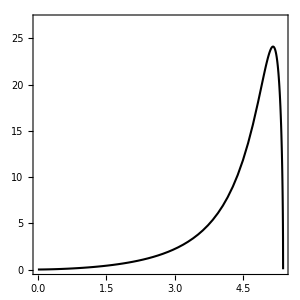

```mathematica
(* differential decay rate *)
(* assign p1=pD1 and p3 = pD2 in both diagrams *)
Tπmax2=(mT^2+mπp^2-(mD0+mD0)^2)/(2mT)-mπp;
plotTπ2=Plot[Module[{m1,m2,m3,pD2Sq,MSq,jacobian,NRnormalization},
m1=mD0;
m2=mD0;
m3=mπp;
pD2Sq=2m2(mT-m1-m2-pD1Sq/(2m1)-√(2m3 T+m3^2));
(*MSq=1/2(8π g^2)/fπ^2(2m3 T)/3 Cos[θ]^2 γ0(1/(pD1Sq+γ0^2)+1/(pD2Sq+γ0^2)(*these momenta stay like they were in the full decay rate*))^2;
jacobian=(2 mT^2)/m1(* new Jacobian reflecting change from pπ^2 -> Subscript[T, π] *);
NRnormalization=(2m1)(2m2)(2mT);*)
NIntegrate[10^3(g^2 m2 m3 T γ0  Cos[θ]^2)/(6 fπ^2 π^2)(1/(pD1Sq+γ0^2)+1/(pD2Sq+γ0^2))^2,{pD1Sq,p1SqMin[m1,m2,m3,2m3 T],p1SqMax[m1,m2,m3,2m3 T]},PrecisionGoal->5]],{T,0,Tπmax2},ImageSize->300,BaseStyle->texStyle,AspectRatio->1,FrameStyle->Black,Frame->True,PlotRange->{0,27},PlotStyle->{Black,Thickness[0.005]}]
```

```mathematica
Grid[{{Rotate[MaTeX["\\frac{d\\Gamma[T_{cc}^+ \\rightarrow D^0 D^0 \\pi^+]}{dT_{\\pi^+}}",Magnification->1.5],90Degree],plotTπ2},{"",MaTeX["T_{\\pi^+}\\;\\text{[MeV]}",Magnification->1.5]}}]
```

-Graphics- | -Graphics-
 | -Graphics-

# T_cc^+→ D^+D^0 γ

## Γ

```mathematica
(* decay rate *)
(* assign p1=pDp and p3 = pD0 in both diagrams *)
photondecay=Module[{m1,m2,m3,pγSq,MSq,jacobian,NRnormalization},
m1=mDp;
m2=0;
m3=mD0;
pγSq=(mT-m1-m3-pDpSq/(2m1)-pD0Sq/(2m3))^2-m2^2;
(*MSq=4π (√2)^2(2pγSq)/3(μp(Cos[θ] √γ0)/(pDpSq+γ0^2)+μ0(Sin[θ] √γp)/(pD0Sq+γp^2))^2;
jacobian=mT^2/(m1 m3);
NRnormalization=(2m1)(2m3)(2mT);*)
NIntegrate[10^3 pγSq/(6 π^2)((√γ0 μp Cos[θ])/(pDpSq+γ0^2)+(√γp μ0 Sin[θ])/(pD0Sq+γp^2))^2,{pD0Sq,p3SqMin[m1,m2,m3],p3SqMax[m1,m2,m3]},{pDpSq,p1SqMin[m1,m2,m3,pD0Sq],p1SqMax[m1,m2,m3,pD0Sq]},PrecisionGoal->5]]
```

6.06968

## dΓ/dE_γ

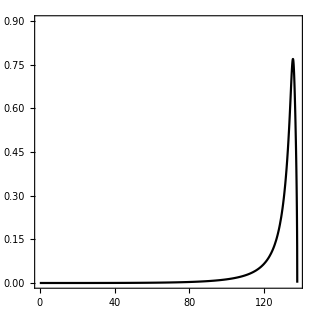

```mathematica
(* differential decay rate *)
(* assign p1=pDp and p2 = pD0 in both diagrams *)
Eγmax1=(mT^2-(mDp+mD0)^2)/(2mT);
photonplot=Plot[Module[{m1,m2,m3,pD0Sq,MSq,jacobian,NRnormalization},
m1=mDp;
m2=mD0;
m3=0;
pD0Sq=2m2(mT-m1-m2-pDpSq/(2m1)-Eγ);
MSq=4π (√2)^2(2 Eγ^2)/3(μp(Cos[θ] √γ0)/(pDpSq+γ0^2)+μ0(Sin[θ] √γp)/(pD0Sq+γp^2))^2;
jacobian=(2 mT^2)/m1;
NRnormalization=(2m1)(2m2)(2mT);
NIntegrate[10^3(Eγ^2 m2)/(3 π^2)((√γ0 μp Cos[θ])/(pDpSq+γ0^2)+(√γp μ0 Sin[θ])/(pD0Sq+γp^2))^2,{pDpSq,γp1SqMin[m1,m2,Eγ],γp1SqMax[m1,m2,Eγ]},PrecisionGoal->5]],{Eγ,0,Eγmax1},ImageSize->315,BaseStyle->texStyle,AspectRatio->1,FrameStyle->Black,Frame->True,PlotRange->{0,0.9},PlotStyle->{Black,Thickness[0.005]}]
```

```mathematica
Grid[{{Rotate[MaTeX["\\frac{d\\Gamma[T_{cc}^+ \\rightarrow D^+ D^0 \\gamma]}{dE_\\gamma}",Magnification->1.5],90Degree],photonplot},{"",MaTeX["E_\\gamma\\;\\text{[MeV]}",Magnification->1.5]}}]
```

-Graphics- | -Graphics-
 | -Graphics-

# Both pion differential plots together

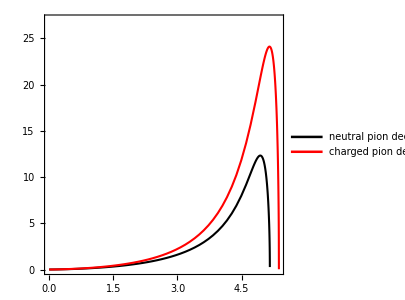

```mathematica
(* differential decay rate *)
(* assign p1=pDp and p3 = pD0 in both diagrams *)
Tπmax1=(mT^2+mπ0^2-(mDp+mD0)^2)/(2mT)-mπ0;
Tπmax2=(mT^2+mπp^2-(mD0+mD0)^2)/(2mT)-mπp;
plotTπ3=Plot[{Module[{m1,m2,m3,pD0Sq,MSq,jacobian,NRnormalization},
m1=mDp;
m2=mD0;
m3=mπ0;
pD0Sq=2m2(mT-m1-m2-pDpSq/(2m1)-√(2m3 T+m3^2));
(*MSq=(4π g^2)/fπ^2 1/3 (2m3 T)((Cos[θ] √γ0)/(pDpSq+γ0^2)-(Sin[θ] √γp)/(pD0Sq+γp^2)(*these momenta stay like they were in the full decay rate*))^2;
jacobian=(2 mT^2)/m1(* new Jacobian reflecting change from pπ^2 -> Subscript[T, π] *);
NRnormalization=(2m1)(2m2)(2mT);*)
NIntegrate[10^3(g^2 m2 m3 T)/(6 fπ^2 π^2)((√γ0 Cos[θ])/(pDpSq+γ0^2)-(√γp Sin[θ])/(pD0Sq+γp^2))^2,{pDpSq,p1SqMin[m1,m2,m3,2m3 T],p1SqMax[m1,m2,m3,2m3 T]},PrecisionGoal->5]],Module[{m1,m2,m3,pD2Sq,MSq,jacobian,NRnormalization},
m1=mD0;
m2=mD0;
m3=mπp;
pD2Sq=2m2(mT-m1-m2-pD1Sq/(2m1)-√(2m3 T+m3^2));
(*MSq=1/2(8π g^2)/fπ^2(2m3 T)/3 Cos[θ]^2 γ0(1/(pD1Sq+γ0^2)+1/(pD2Sq+γ0^2)(*these momenta stay like they were in the full decay rate*))^2;
jacobian=(2 mT^2)/m1(* new Jacobian reflecting change from pπ^2 -> Subscript[T, π] *);
NRnormalization=(2m1)(2m2)(2mT);*)
NIntegrate[10^3(g^2 m2 m3 T γ0  Cos[θ]^2)/(6 fπ^2 π^2)(1/(pD1Sq+γ0^2)+1/(pD2Sq+γ0^2))^2,{pD1Sq,p1SqMin[m1,m2,m3,2m3 T],p1SqMax[m1,m2,m3,2m3 T]},PrecisionGoal->5]]},{T,0,If[Tπmax1>Tπmax2,Tπmax1,Tπmax2]},ImageSize->300,BaseStyle->texStyle,AspectRatio->1,FrameStyle->Black,Frame->True,PlotRange->{0,27},PlotStyle->{{Black,Thickness[0.005]},{Red,Thickness[0.005]}},PlotLegends->Placed[{"neutral pion decay","charged pion decay"},{Left,Center}]]
```

```mathematica
Grid[{{Rotate[MaTeX["\\frac{d\\Gamma}{dT_\\pi}",Magnification->1.5],90Degree],plotTπ3},{"",MaTeX["T_\\pi\\;\\text{[MeV]}",Magnification->1.5]}}]
```

-Graphics- | -Graphics-
 | -Graphics-

# Distribution as a function of m_DD

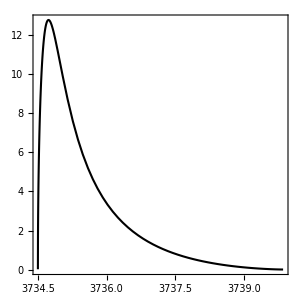

```mathematica
(* differential decay rate *)
(* assign p1=pDp and p2 = pD0 in both diagrams *)
Plot[Module[{m1,m2,m3,pD0Sq,T,MSq,jacobian,NRnormalization},
m1=mDp;
m2=mD0;
m3=mπ0;
pD0Sq=2m2(mT-m1-m2-pDpSq/(2m1)-√(2m3 T+m3^2));
T=(mT^2-mDD^2+mπ0^2)/(2mT)-mπ0;
NIntegrate[mT/mDD 10^3(g^2 m2 m3 T)/(6 fπ^2 π^2)((√γ0 Cos[θ])/(pDpSq+γ0^2)-(√γp Sin[θ])/(pD0Sq+γp^2))^2,{pDpSq,p1SqMin[m1,m2,m3,2m3 T],p1SqMax[m1,m2,m3,2m3 T]},PrecisionGoal->5]],{mDD,mD0+mDp,mT-mπ0},ImageSize->300,BaseStyle->texStyle,AspectRatio->1,FrameStyle->Black,Frame->True,PlotStyle->{Black,Thickness[0.005]}]
```

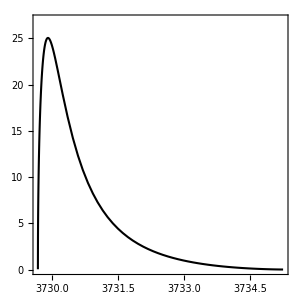

```mathematica
(* differential decay rate *)
(* assign p1=pD1 and p3 = pD2 in both diagrams *)
Plot[Module[{m1,m2,m3,pD2Sq,T,MSq,jacobian,NRnormalization},
m1=mD0;
m2=mD0;
m3=mπp;
pD2Sq=2m2(mT-m1-m2-pD1Sq/(2m1)-√(2m3 T+m3^2));
T=(mT^2-mDD^2+mπp^2)/(2mT)-mπp;
NIntegrate[mT/mDD 10^3(g^2 m2 m3 T γ0  Cos[θ]^2)/(6 fπ^2 π^2)(1/(pD1Sq+γ0^2)+1/(pD2Sq+γ0^2))^2,{pD1Sq,p1SqMin[m1,m2,m3,2m3 T],p1SqMax[m1,m2,m3,2m3 T]},PrecisionGoal->5]],{mDD,2mD0,mT-mπp},ImageSize->300,BaseStyle->texStyle,AspectRatio->1,FrameStyle->Black,Frame->True,PlotRange->{0,27},PlotStyle->{Black,Thickness[0.005]}]
```

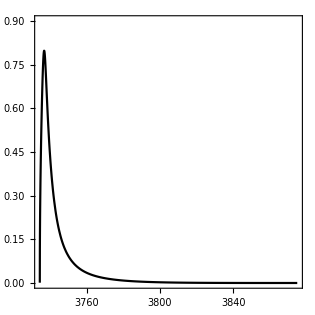

```mathematica
Plot[Module[{m1,m2,m3,pD0Sq,MSq,Eγ,jacobian,NRnormalization},
m1=mDp;
m2=mD0;
m3=0;
pD0Sq=2m2(mT-m1-m2-pDpSq/(2m1)-Eγ);
MSq=4π (√2)^2(2 Eγ^2)/3(μp(Cos[θ] √γ0)/(pDpSq+γ0^2)+μ0(Sin[θ] √γp)/(pD0Sq+γp^2))^2;
jacobian=(2 mT^2)/m1;
NRnormalization=(2m1)(2m2)(2mT);
Eγ=(mT^2-mDD^2)/(2mT);
NIntegrate[mT/mDD 10^3(Eγ^2 m2)/(3 π^2)((√γ0 μp Cos[θ])/(pDpSq+γ0^2)+(√γp μ0 Sin[θ])/(pD0Sq+γp^2))^2,{pDpSq,γp1SqMin[m1,m2,Eγ],γp1SqMax[m1,m2,Eγ]},PrecisionGoal->5]],{mDD,mD0+mDp,mT},ImageSize->315,BaseStyle->texStyle,AspectRatio->1,FrameStyle->Black,Frame->True,PlotRange->{0,0.9},PlotStyle->{Black,Thickness[0.005]}]
```

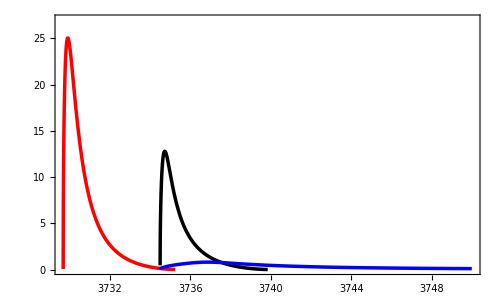

```mathematica
Plot[{Module[{m1,m2,m3,pD0Sq,T,MSq,jacobian,NRnormalization},
m1=mDp;
m2=mD0;
m3=mπ0;
pD0Sq=2m2(mT-m1-m2-pDpSq/(2m1)-√(2m3 T+m3^2));
T=(mT^2-mDD^2+mπ0^2)/(2mT)-mπ0;
NIntegrate[mT/mDD 10^3(g^2 m2 m3 T)/(6 fπ^2 π^2)((√γ0 Cos[θ])/(pDpSq+γ0^2)-(√γp Sin[θ])/(pD0Sq+γp^2))^2,{pDpSq,p1SqMin[m1,m2,m3,2m3 T],p1SqMax[m1,m2,m3,2m3 T]},PrecisionGoal->5]],Module[{m1,m2,m3,pD2Sq,T,MSq,jacobian,NRnormalization},
m1=mD0;
m2=mD0;
m3=mπp;
pD2Sq=2m2(mT-m1-m2-pD1Sq/(2m1)-√(2m3 T+m3^2));
T=(mT^2-mDD^2+mπp^2)/(2mT)-mπp;
NIntegrate[mT/mDD 10^3(g^2 m2 m3 T γ0  Cos[θ]^2)/(6 fπ^2 π^2)(1/(pD1Sq+γ0^2)+1/(pD2Sq+γ0^2))^2,{pD1Sq,p1SqMin[m1,m2,m3,2m3 T],p1SqMax[m1,m2,m3,2m3 T]},PrecisionGoal->5]],Module[{m1,m2,m3,pD0Sq,MSq,Eγ,jacobian,NRnormalization},
m1=mDp;
m2=mD0;
m3=0;
pD0Sq=2m2(mT-m1-m2-pDpSq/(2m1)-Eγ);
MSq=4π (√2)^2(2 Eγ^2)/3(μp(Cos[θ] √γ0)/(pDpSq+γ0^2)+μ0(Sin[θ] √γp)/(pD0Sq+γp^2))^2;
jacobian=(2 mT^2)/m1;
NRnormalization=(2m1)(2m2)(2mT);
Eγ=(mT^2-mDD^2)/(2mT);
NIntegrate[mT/mDD 10^3(Eγ^2 m2)/(3 π^2)((√γ0 μp Cos[θ])/(pDpSq+γ0^2)+(√γp μ0 Sin[θ])/(pD0Sq+γp^2))^2,{pDpSq,γp1SqMin[m1,m2,Eγ],γp1SqMax[m1,m2,Eγ]},PrecisionGoal->5]]},{mDD,2mD0,3750},ImageSize->500,BaseStyle->texStyle,AspectRatio->0.6,FrameStyle->Black,Frame->True,PlotRange->{0,27},PlotStyle->{{Black,Thickness[0.005]},{Red,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotLegends->Placed[{MaTeX["T_{cc}^+ \\rightarrow D^+ D^0 \\pi^0",Magnification->1.5],MaTeX["T_{cc}^+ \\rightarrow D^0 D^0 \\pi^+",Magnification->1.5],MaTeX["T_{cc}^+ \\rightarrow D^+ D^0 \\gamma",Magnification->1.5]},{Right,Top}]]
```

```mathematica
Grid[{{Rotate[MaTeX["\\frac{d\\Gamma}{dm_{DD}}",Magnification->1.5],90Degree],%101},{"",MaTeX["m_{DD}\\;\\text{[MeV]}",Magnification->1.5]}}]
```

-Graphics- | -Graphics-
 | -Graphics-

# Total decay rate

```mathematica
(* Γ (keV) *)
neutralpiondecay+chargedpiondecay+chargedDphotondecay
```

35.4845+chargedDphotondecay

# Total decay width as a function of theta

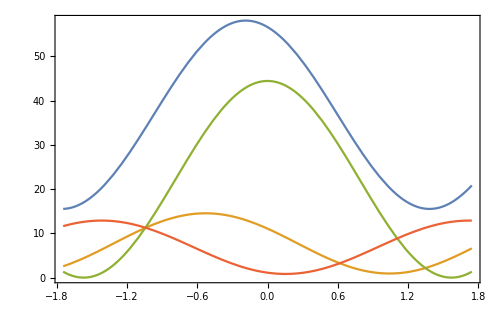

```mathematica
Plot[{Module[{m1,m2,m3,pπSq,MSq,jacobian,NRnormalization},
m1=mDp;
m2=mπ0;
m3=mD0;
pπSq=(mT-m1-m3-pDpSq/(2m1)-pD0Sq/(2m3))^2-m2^2;
(*MSq=(4π g^2)/fπ^2 pπSq/3((Cos[θ] √γ0)/(pDpSq+γ0^2)-(Sin[θ] √γp)/(pD0Sq+γp^2))^2;
jacobian=mT^2/(m1 m3);
NRnormalization=(2m1)(2m3)(2mT);*)
NIntegrate[10^3(* to make result in keV *)(g^2 pπSq)/(24 fπ^2 π^2)((√γ0 Cos[θ])/(pDpSq+γ0^2)-(√γp Sin[θ])/(pD0Sq+γp^2))^2,{pD0Sq,p3SqMin[m1,m2,m3],p3SqMax[m1,m2,m3]},{pDpSq,p1SqMin[m1,m2,m3,pD0Sq],p1SqMax[m1,m2,m3,pD0Sq]},PrecisionGoal->5]]+Module[{m1,m2,m3,pπSq,MSq,jacobian,NRnormalization},
m1=mD0;
m2=mπp;
m3=mD0;
pπSq=(mT-m1-m3-pD1Sq/(2m1)-pD2Sq/(2m3))^2-m2^2;
(*MSq=1/2(8π g^2)/fπ^2 pπSq/3 Cos[θ]^2 γ0(1/(pD1Sq+γ0^2)+1/(pD2Sq+γ0^2))^2;
jacobian=mT^2/(m1 m3);
NRnormalization=(2m1)(2m3)(2mT);*)
NIntegrate[10^3(g^2 pπSq γ0  Cos[θ]^2)/(24 fπ^2 π^2)(1/(pD1Sq+γ0^2)+1/(pD2Sq+γ0^2))^2,{pD2Sq,p3SqMin[m1,m2,m3],p3SqMax[m1,m2,m3]},{pD1Sq,p1SqMin[m1,m2,m3,pD2Sq],p1SqMax[m1,m2,m3,pD2Sq]},PrecisionGoal->5]]+Module[{m1,m2,m3,pγSq,MSq,jacobian,NRnormalization},
m1=mDp;
m2=0;
m3=mD0;
pγSq=(mT-m1-m3-pDpSq/(2m1)-pD0Sq/(2m3))^2-m2^2;
(*MSq=4π (√2)^2(2pγSq)/3(μp(Cos[θ] √γ0)/(pDpSq+γ0^2)+μ0(Sin[θ] √γp)/(pD0Sq+γp^2))^2;
jacobian=mT^2/(m1 m3);
NRnormalization=(2m1)(2m3)(2mT);*)
NIntegrate[10^3 pγSq/(6 π^2)((√γ0 μp Cos[θ])/(pDpSq+γ0^2)+(√γp μ0 Sin[θ])/(pD0Sq+γp^2))^2,{pD0Sq,p3SqMin[m1,m2,m3],p3SqMax[m1,m2,m3]},{pDpSq,p1SqMin[m1,m2,m3,pD0Sq],p1SqMax[m1,m2,m3,pD0Sq]},PrecisionGoal->5]],Module[{m1,m2,m3,pπSq,MSq,jacobian,NRnormalization},
m1=mDp;
m2=mπ0;
m3=mD0;
pπSq=(mT-m1-m3-pDpSq/(2m1)-pD0Sq/(2m3))^2-m2^2;
(*MSq=(4π g^2)/fπ^2 pπSq/3((Cos[θ] √γ0)/(pDpSq+γ0^2)-(Sin[θ] √γp)/(pD0Sq+γp^2))^2;
jacobian=mT^2/(m1 m3);
NRnormalization=(2m1)(2m3)(2mT);*)
NIntegrate[10^3(* to make result in keV *)(g^2 pπSq)/(24 fπ^2 π^2)((√γ0 Cos[θ])/(pDpSq+γ0^2)-(√γp Sin[θ])/(pD0Sq+γp^2))^2,{pD0Sq,p3SqMin[m1,m2,m3],p3SqMax[m1,m2,m3]},{pDpSq,p1SqMin[m1,m2,m3,pD0Sq],p1SqMax[m1,m2,m3,pD0Sq]},PrecisionGoal->5]],Module[{m1,m2,m3,pπSq,MSq,jacobian,NRnormalization},
m1=mD0;
m2=mπp;
m3=mD0;
pπSq=(mT-m1-m3-pD1Sq/(2m1)-pD2Sq/(2m3))^2-m2^2;
(*MSq=1/2(8π g^2)/fπ^2 pπSq/3 Cos[θ]^2 γ0(1/(pD1Sq+γ0^2)+1/(pD2Sq+γ0^2))^2;
jacobian=mT^2/(m1 m3);
NRnormalization=(2m1)(2m3)(2mT);*)
NIntegrate[10^3(g^2 pπSq γ0  Cos[θ]^2)/(24 fπ^2 π^2)(1/(pD1Sq+γ0^2)+1/(pD2Sq+γ0^2))^2,{pD2Sq,p3SqMin[m1,m2,m3],p3SqMax[m1,m2,m3]},{pD1Sq,p1SqMin[m1,m2,m3,pD2Sq],p1SqMax[m1,m2,m3,pD2Sq]},PrecisionGoal->5]],Module[{m1,m2,m3,pγSq,MSq,jacobian,NRnormalization},
m1=mDp;
m2=0;
m3=mD0;
pγSq=(mT-m1-m3-pDpSq/(2m1)-pD0Sq/(2m3))^2-m2^2;
(*MSq=4π (√2)^2(2pγSq)/3(μp(Cos[θ] √γ0)/(pDpSq+γ0^2)+μ0(Sin[θ] √γp)/(pD0Sq+γp^2))^2;
jacobian=mT^2/(m1 m3);
NRnormalization=(2m1)(2m3)(2mT);*)
NIntegrate[10^3 pγSq/(6 π^2)((√γ0 μp Cos[θ])/(pDpSq+γ0^2)+(√γp μ0 Sin[θ])/(pD0Sq+γp^2))^2,{pD0Sq,p3SqMin[m1,m2,m3],p3SqMax[m1,m2,m3]},{pDpSq,p1SqMin[m1,m2,m3,pD0Sq],p1SqMax[m1,m2,m3,pD0Sq]},PrecisionGoal->5]]},{θ,-100Degree,100Degree},ImageSize->500,BaseStyle->texStyle,FrameStyle->Black,Frame->True,PlotLegends->Placed[{MaTeX["\\text{All decays}",Magnification->1.5],MaTeX["T_{cc}^+ \\rightarrow D^+ D^0 \\pi^0",Magnification->1.5],MaTeX["T_{cc}^+ \\rightarrow D^0 D^0 \\pi^+",Magnification->1.5],MaTeX["T_{cc}^+ \\rightarrow D^+ D^0 \\gamma",Magnification->1.5]},{Right,Top}]]
```

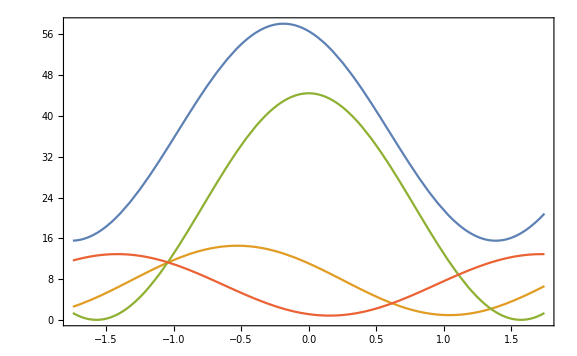
-Graphics- | -Graphics-
 | -Graphics-

```mathematica
Grid[{{Rotate[MaTeX["\\Gamma",Magnification->1.5],90Degree],%62},{"",MaTeX["\\theta",Magnification->1.5]}}]
```

# Three-point integrals

```mathematica
F[a_,b_,c_]:=1/(√c)(ArcSin[b/(√(b^2+4a c))]-ArcSin[(b-2c)/(√(b^2+4a c))])(*1503.02719*)
μij[mi_,mj_]:=(mi mj)/(mi+mj)
γ12[m1_,m2_]:=√(2μij[m1,m2](m1+m2-mT))
γ13[m1_,m3_,b_]:=√(2μij[m1,m3](m1+m3-(m1+m3-b)))
```

```mathematica
(* Tcc+ -> Tcc+squig π0 *)
f1[b_]:=
Module[{pπ,mTsquig,Esquig},
mTsquig=mD0+mDp-b;
pπ=√(((mT^2+mπ0^2-mTsquig^2)/(2mT))^2-mπ0^2);
Esquig=√(pπ^2+mTsquig^2);
10^3(pπ mTsquig)/(2π mT)pπ^2/3 Abs[g/(√2 fπ)(Cos[θ] √(γ12[mD0,mDps]γ13[mD0,mDp,b])F[γ12[mD0,mDps]^2,pπ^2 μij[mD0,mDp]/mDp(*+γ13[mD0,mDp,b]^2*)+2μij[mD0,mDp](mD0+mDp-Esquig)-γ12[mD0,mDps]^2,μij[mD0,mDp]^2/mDp^2 pπ^2]-Sin[θ] √(γ12[mDp,mD0s]γ13[mDp,mD0,b])F[γ12[mDp,mD0s]^2,pπ^2 μij[mDp,mD0]/mD0(*+γ13[mDp,mD0,b]^2*)+2μij[mDp,mD0](mDp+mD0-Esquig)-γ12[mDp,mD0s]^2,μij[mDp,mD0]^2/mD0^2 pπ^2])]^2
]
```

```mathematica
loopneutralpion=f1[2]
```

61.4047

```mathematica
(* Tcc+ -> Tcc0squig π+ *)
f2[b_]:=
Module[{pπ,mTsquig,Esquig},
mTsquig=2mD0-b;
pπ=√(((mT^2+mπp^2-mTsquig^2)/(2mT))^2-mπp^2);
Esquig=√(pπ^2+mTsquig^2);
10^3(pπ mTsquig)/(2π mT)pπ^2/3 Abs[g/fπ(Cos[θ] √(γ12[mD0,mDps]γ13[mD0,mD0,b])F[γ12[mD0,mDps]^2,pπ^2 μij[mD0,mD0]/mD0(*+γ13[mD0,mD0,b]^2*)+2μij[mD0,mD0](mD0+mD0-Esquig)-γ12[mD0,mDps]^2,μij[mD0,mD0]^2/mD0^2 pπ^2])]^2
]
```

```mathematica
loopchargedpion=f2[2]
```

45.4417

```mathematica
(* Tcc+ -> Tcc+squig γ *)
f3[b_]:=
Module[{pγ,mTsquig,Esquig},
mTsquig=mD0+mDp-b;
pγ=√(((mT^2-mTsquig^2)/(2mT))^2);
Esquig=√(pγ^2+mTsquig^2);
10^3(pγ mTsquig)/(2π mT)(2 pγ^2)/3 Abs[(μp Cos[θ] √(γ12[mD0,mDps]γ13[mD0,mDp,b])F[γ12[mD0,mDps]^2,pγ^2 μij[mD0,mDp]/mDp(*+γ13[mD0,mDp,b]^2*)+2μij[mD0,mDp](mD0+mDp-Esquig)-γ12[mD0,mDps]^2,μij[mD0,mDp]^2/mDp^2 pγ^2]+μ0 Sin[θ] √(γ12[mDp,mD0s]γ13[mDp,mD0,b])F[γ12[mDp,mD0s]^2,pγ^2 μij[mDp,mD0]/mD0(*+γ13[mDp,mD0,b]^2*)+2μij[mDp,mD0](mDp+mD0-Esquig)-γ12[mDp,mD0s]^2,μij[mDp,mD0]^2/mD0^2 pγ^2])]^2
]
```

```mathematica
loopphoton=f3[2]
```

2.29592

```mathematica
chargedpiondecay+neutralpiondecay+photondecay+loopchargedpion+loopneutralpion+loopphoton
```

161.529

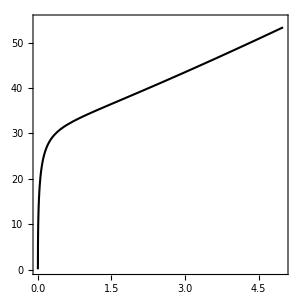

```mathematica
Plot[f1[b],{b,0,5},ImageSize->300,BaseStyle->texStyle,AspectRatio->1,FrameStyle->Black,Frame->True,PlotStyle->{Black,Thickness[0.005]},PlotRange->{0,55}]
```

```mathematica
Grid[{{Rotate[MaTeX["\\Gamma[T_{cc}^+ \\rightarrow \\tilde{T}_{cc}^+ \\pi^0] \\; [\\text{keV}]",Magnification->1.5],90Degree],%159},{"",MaTeX["\\tilde{T}_{cc}^+ \; \\text{binding energy} \\; [\\text{MeV}]",Magnification->1.5]}}]
```

-Graphics- | -Graphics-
 | -Graphics-

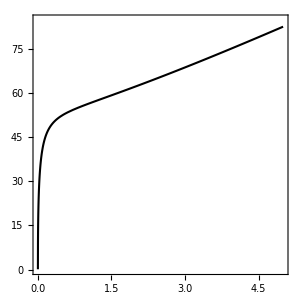

```mathematica
Plot[f2[b],{b,0,5},ImageSize->300,BaseStyle->texStyle,AspectRatio->1,FrameStyle->Black,Frame->True,PlotStyle->{Black,Thickness[0.005]},PlotRange->{0,85}]
```

```mathematica
Grid[{{Rotate[MaTeX["\\Gamma[T_{cc}^+ \\rightarrow \\tilde{T}_{cc}^0 \\pi^+] \\; [\\text{keV}]",Magnification->1.5],90Degree],%162},{"",MaTeX["\\tilde{T}_{cc}^0 \; \\text{binding energy} \\; [\\text{MeV}]",Magnification->1.5]}}]
```

-Graphics- | -Graphics-
 | -Graphics-

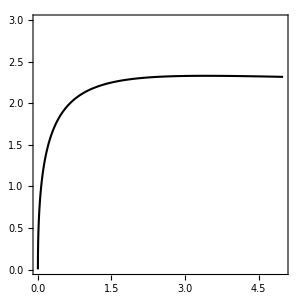

```mathematica
Plot[f3[b],{b,0,5},ImageSize->300,BaseStyle->texStyle,AspectRatio->1,FrameStyle->Black,Frame->True,PlotStyle->{Black,Thickness[0.005]},PlotRange->{0,3}]
```

```mathematica
Grid[{{Rotate[MaTeX["\\Gamma[T_{cc}^+ \\rightarrow \\tilde{T}_{cc}^+ \\gamma] \\; [\\text{keV}]",Magnification->1.5],90Degree],%165},{"",MaTeX["\\tilde{T}_{cc}^+ \; \\text{binding energy} \\; [\\text{MeV}]",Magnification->1.5]}}]
```

-Graphics- | -Graphics-
 | -Graphics-

# Experimental data from LHCb

```mathematica
(* data courtesy of Mikhail Mikhasenko.  From him: "Please be aware that these are the representation of the binned data, while we do unbinned likelihood fits in our studies. There might be a loss of precision due to binning." 
*)
```

```mathematica
fig4aXaxis={3.72991,3.73041,3.73091,3.73141,3.73191,3.73241,3.73291,3.73341,3.73391,3.73441,3.73491,3.73541,3.73591,3.73641,3.73691,3.73741,3.73791,3.73841,3.73891,3.73941,3.73991,3.74041,3.74091,3.74141,3.74191,3.74241,3.74291,3.74341,3.74391,3.74441,3.74491,3.74541,3.74591,3.74641,3.74691,3.74741,3.74791,3.74841,3.74891,3.74941,3.74991,3.75041,3.75091,3.75141,3.75191,3.75241,3.75291,3.75341,3.75391,3.75441,3.75491,3.75541,3.75591,3.75641,3.75691,3.75741};
fig4aYaxis={91.87349,83.91322,43.65984,32.40545,22.15956,24.21192,22.38146,16.05066,20.61709,17.76958,15.275,6.41135,14.74418,16.74665,17.8299,11.3512,33.12155,18.3281,20.66652,20.65011,15.08982,15.46257,31.60039,22.50674,10.46671,7.849067,9.293681,15.61505,19.17972,5.768346,18.83466,10.71483,22.12074,11.89772,18.42971,13.30208,17.09842,16.30606,24.00543,27.09684,12.30812,27.87209,13.9568,21.87492,34.95869,20.41001,23.9531,19.04171,24.03083,18.4567,15.25985,21.42472,25.46886,18.04251,23.55832,21.16552};
fig4aError={10.9283,10.09399,7.560818,7.044639,5.961235,6.237155,5.864415,5.043657,6.133625,5.610891,5.627861,4.378205,5.827929,5.712013,5.695677,5.36071,6.790226,6.175454,6.298213,5.975063,5.693189,6.22815,7.128134,6.42513,5.541696,5.42431,5.049529,5.836657,6.207817,5.204006,6.31746,5.121723,6.512871,5.813573,6.370801,6.086546,6.390469,5.966866,6.841243,7.072078,6.421888,7.250396,5.791154,6.567666,7.844,7.001333,6.626488,6.174498,6.605388,6.242446,6.41643,6.557458,6.923712,6.096799,7.202532,6.598221};
fig4aBkgrdPoints(*from WebPlotDigitizer*)={{3.7302171428571427,4.752623688155921},{3.7304914285714283,5.689655172413779},{3.7311085714285714,7.751124437781101},{3.7314171428571425,8.500749625187382},{3.732137142857143,10},{3.732445714285714,10.562218890554703},{3.733165714285714,11.686656671664167},{3.733508571428571,12.248875562218899},{3.734262857142857,13.185907046476757},{3.7354285714285713,14.49775112443777},{3.7366971428571425,15.434782608695627},{3.7379314285714282,16.55922038980509},{3.739268571428571,17.496251874062963},{3.7402971428571425,17.87106446776609},{3.741805714285714,18.6206896551724},{3.743245714285714,19.18290854572713},{3.745028571428571,19.557721139430285},{3.746365714285714,19.932533733133425},{3.747702857142857,20.119940029985003},{3.7496571428571426,20.307346326836566},{3.751611428571428,20.307346326836566},{3.7535314285714283,20.307346326836566},{3.755245714285714,20.119940029985003},{3.756788571428571,19.745127436281862}};
fig4a=Table[{1000fig4aXaxis[[i]],Around[fig4aYaxis[[i]]-Interpolation[fig4aBkgrdPoints,fig4aXaxis[[i]]],fig4aError[[i]]]},{i,1,Length[fig4aXaxis]}];
fig4bXaxis={3.73473,3.73523,3.73573,3.73623,3.73673,3.73723,3.73773,3.73823,3.73873,3.73923,3.73973,3.74023,3.74073,3.74123,3.74173,3.74223,3.74273,3.74323,3.74373,3.74423,3.74473,3.74523,3.74573,3.74623,3.74673,3.74723,3.74773,3.74823,3.74873,3.74923,3.74973,3.75023,3.75073,3.75123,3.75173,3.75223,3.75273,3.75323,3.75373,3.75423,3.75473,3.75523,3.75573,3.75623,3.75673,3.75723};
fig4bYaxis={38.04047,36.18541,40.80066,30.92631,14.30568,28.23303,23.64475,19.0599,16.53869,23.00334,17.32386,9.817419,24.99132,19.97771,8.07264,34.64889,23.34397,27.00311,18.80671,18.57994,17.62958,14.99337,11.93305,25.45009,12.78334,16.77578,9.714108,12.36677,12.338,24.68596,7.384336,19.38121,32.93354,19.76261,13.48532,20.70776,15.48021,21.8253,24.46633,20.61676,17.59626,12.46061,17.51616,30.63834,7.505555,19.3337};
fig4bError={7.464232,7.242437,7.460643,6.965002,5.898423,6.267186,6.621599,6.014302,6.137484,6.423124,6.289081,5.65899,6.90446,7.104523,5.728642,7.965738,6.622948,7.251705,5.89567,7.252382,6.872203,6.251087,6.331838,6.776095,6.21899,6.613073,5.826992,6.449921,5.899172,7.436035,6.053245,6.339896,7.859357,6.784779,6.216847,7.007693,6.162625,6.932399,7.224195,7.043905,7.136549,6.878359,6.447563,7.354987,6.327336,7.543988};
fig4bBkgrdPoints(*from WebPlotDigitizer*)={{3.7346105263157896,3.0322580645161423},{3.734778947368421,4.246334310850443},{3.735143859649123,6.404692082111438},{3.7353684210526317,7.348973607038133},{3.7358175438596493,8.967741935483886},{3.7361263157894737,9.777126099706749},{3.7365754385964913,10.991202346041064},{3.7369122807017545,11.665689149560123},{3.7373894736842104,12.609970674486803},{3.7377263157894736,13.149560117302059},{3.73820350877193,13.958944281524921},{3.7385684210526318,14.498533724340191},{3.7390736842105263,15.173020527859236},{3.7394385964912282,15.577712609970689},{3.739943859649123,16.117302052785917},{3.7403087719298247,16.38709677419355},{3.7408140350877193,16.79178885630499},{3.741178947368421,17.196480938416414},{3.7416842105263157,17.46627565982405},{3.742021052631579,17.736070381231684},{3.742554385964912,18.005865102639305},{3.742919298245614,18.27565982404691},{3.7434245614035087,18.41055718475073},{3.7443508771929825,18.815249266862182},{3.7446877192982457,18.950146627565985},{3.7451929824561403,19.085043988269803},{3.745557894736842,19.21994134897362},{3.7460912280701755,19.35483870967741},{3.7464280701754387,19.35483870967741},{3.74698947368421,19.35483870967741},{3.7473263157894734,19.489736070381227},{3.7478596491228067,19.489736070381227},{3.7481684210526316,19.624633431085044},{3.748757894736842,19.489736070381227},{3.749094736842105,19.489736070381227},{3.7496,19.35483870967741},{3.7499649122807015,19.35483870967741},{3.7505263157894735,19.21994134897362},{3.7508631578947367,19.085043988269803},{3.7513684210526312,18.950146627565985},{3.7519298245614032,18.950146627565985},{3.7528842105263154,18.41055718475073},{3.7542035087719294,18.005865102639305},{3.7552982456140347,17.601173020527867},{3.7562245614035086,17.196480938416414},{3.7569263157894732,16.52199413489737}};
fig4b=Table[{1000fig4bXaxis[[i]],Around[fig4bYaxis[[i]]-Interpolation[fig4bBkgrdPoints,fig4bXaxis[[i]]],fig4bError[[i]]]},{i,1,Length[fig4bXaxis]}];
```

InterpolatingFunction::dmval: Input value {3.72991} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.75691} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.75741} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.75723} lies outside the range of data in the interpolating function. Extrapolation will be used.

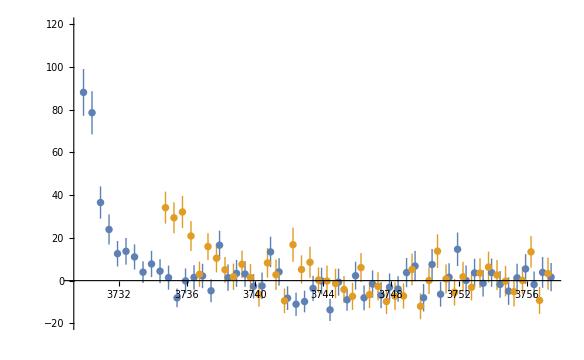

```mathematica
RawDataPlot=ListPlot[{fig4a,fig4b},PlotRange->{-20,120},PlotLegends->Placed[{MaTeX["D^0 D^0 \;\\text{final state data}",Magnification->1.2],MaTeX["D^+ D^0 \;\\text{final state data}",Magnification->1.2]},{Right,Top}]]
```

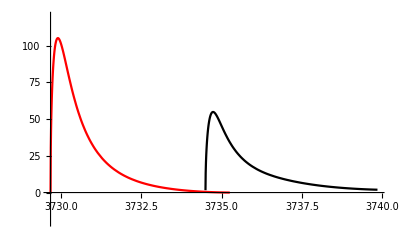

```mathematica
factor=4.2;
EFTplot=Plot[{Module[{m1,m2,m3,pD0Sq,T,MSq,jacobian,NRnormalization},
m1=mDp;
m2=mD0;
m3=mπ0;
pD0Sq=2m2(mT-m1-m2-pDpSq/(2m1)-√(2m3 T+m3^2));
T=(mT^2-mDD^2+mπ0^2)/(2mT)-mπ0;
NIntegrate[factor(*multiplicative factor to match raw data normalization*)mT/mDD 10^3(g^2 m2 m3 T)/(6 fπ^2 π^2)((√γ0 Cos[θ])/(pDpSq+γ0^2)-(√γp Sin[θ])/(pD0Sq+γp^2))^2,{pDpSq,p1SqMin[m1,m2,m3,2m3 T],p1SqMax[m1,m2,m3,2m3 T]},PrecisionGoal->5]]+Module[{m1,m2,m3,pD0Sq,MSq,Eγ,jacobian,NRnormalization},
m1=mDp;
m2=mD0;
m3=0;
pD0Sq=2m2(mT-m1-m2-pDpSq/(2m1)-Eγ);
MSq=4π (√2)^2(2 Eγ^2)/3(μp(Cos[θ] √γ0)/(pDpSq+γ0^2)+μ0(Sin[θ] √γp)/(pD0Sq+γp^2))^2;
jacobian=(2 mT^2)/m1;
NRnormalization=(2m1)(2m2)(2mT);
Eγ=(mT^2-mDD^2)/(2mT);
NIntegrate[factor(*multiplicative factor to match raw data normalization*)mT/mDD 10^3(Eγ^2 m2)/(3 π^2)((√γ0 μp Cos[θ])/(pDpSq+γ0^2)+(√γp μ0 Sin[θ])/(pD0Sq+γp^2))^2,{pDpSq,γp1SqMin[m1,m2,Eγ],γp1SqMax[m1,m2,Eγ]},PrecisionGoal->5]],Module[{m1,m2,m3,pD2Sq,T,MSq,jacobian,NRnormalization},
m1=mD0;
m2=mD0;
m3=mπp;
pD2Sq=2m2(mT-m1-m2-pD1Sq/(2m1)-√(2m3 T+m3^2));
T=(mT^2-mDD^2+mπp^2)/(2mT)-mπp;
NIntegrate[factor(*multiplicative factor to match raw data normalization*)mT/mDD 10^3(g^2 m2 m3 T γ0  Cos[θ]^2)/(6 fπ^2 π^2)(1/(pD1Sq+γ0^2)+1/(pD2Sq+γ0^2))^2,{pD1Sq,p1SqMin[m1,m2,m3,2m3 T],p1SqMax[m1,m2,m3,2m3 T]},PrecisionGoal->5]]},{mDD,2mD0,3756},PlotRange->{-20,120},PlotStyle->{Black,Red},PlotLegends->Placed[{MaTeX["\\begin{aligned}
&4.2\\times\\Gamma'[T_{cc}^+ \\rightarrow D^+ D^0 \\pi^0] \\\\  + & 4.2\\times \\Gamma'[T_{cc}^+ \\rightarrow D^+ D^0 \\gamma]
\\end{aligned}",Magnification->1.2],MaTeX["\; \; \; 4.2\\times\\Gamma'[T_{cc}^+ \\rightarrow D^0 D^0 \\pi^+]",Magnification->1.2]},{Right,Top}]]
```

```mathematica
togetherplot=Show[RawDataPlot,EFTplot,ImageSize->500,BaseStyle->texStyle,AspectRatio->0.5,FrameStyle->Black,Frame->True]
```

-Graphics-

```mathematica
Grid[{{Rotate[MaTeX["\\text{Yield}/(500 \\; \\text{keV})",Magnification->1.5],90Degree],togetherplot},{"",MaTeX["m_{DD} \\; [\\text{MeV}]",Magnification->1.5]}}]
```

-Graphics- | -Graphics-
 | -Graphics-